CP1-1: Calculating derivatives with Mathematica

This exercise demonstrates how Mathematica can be used to calculate the first, second or third derivative of a function.

This notebook also demonstrates how a Mathematica notebook can be organized into sections and subsections. For the present example, such a structure is of little extra value, but in case of more complex projects a good organisation of your notebooks may be of crucial importance. You can make a section or subsection by selecting a new plain text cell and formatting it as a (sub) section with Format → Style → Section in the menu bar. To open or close a given section, click on the arrow next to its header. [Try it!!] Inserting an expression group or a text paragraph within a section works much the same way, for example with Format → Style → Subsection. For this, you can also use the keyboard shortcuts Alt+4, Alt+5, Alt+6 for sections, subsections and subsubsections, respectively. You can delete cells or sections by selecting the enclosing bar on the right and pressing DELETE.

You can work systematically through a pre-made notebook by executing the commands one by one by pressing SHIFT+ENTER. It is important to work through the sheet in ‘chronological order’ (i.e.from top to bottom) as some variables are assigned different values in the process. It is advisable to start every notebook with the command Quit[] that clears the memory of Mathematica:

```mathematica
Quit[]
```

### Introduction: Differentiation with Mathematica

In Mathematica, the command D[] is used for calculating derivatives. For example, D[f,x] is the first order derivative of a function f with respect to the variable x. Higher order derivatives can be calculated by expanding the second argument like D[f,x,x] to compute the second order derivative of f or D[f,x,x,x] to calculate the third derivative of f.  Alternatively, the command D[f,{x,k}] can be used to calculate the k-th order derivative of f with respect to x. Hence, 
D[f,{x,2}] is an alternative way to specify the second order derivative of f.

Let us now demonstrate how a simple function like f(x)=4 x^2+4x+1 can be differentiated with Mathematica. A simple way to calculate the first three derivatives would be:

```mathematica
D[4*x^2+4*x+1,x]
D[4*x^2+4*x+1,x,x]
D[4*x^2+4*x+1,x,x,x]
```

Alternatively, using the D[f,{x,k}] notation:

```mathematica
D[4*x^2+4*x+1,{x,1}]
D[4*x^2+4*x+1,{x,2}]
D[4*x^2+4*x+1,{x,3}]
```

The above way of entering the same term 4 x^2+4x+1 into several commands is tedious and error-prone. It is therefore advisable to give this term a name. The standard way to do so is:

```mathematica
f=4*x^2+4*x+1
```

You can now simply calculate the desired derivatives:

```mathematica
D[f,{x,1}]
D[f,{x,2}]
D[f,{x,3}]
```

Sometimes it is useful to give these derivatives a name, since you can then later perform some operation on the derivatives (like plotting them). It does not matter which name you choose: first-derivative=D[f,x] is as acceptable as df=D[f,x]. In our case, we get:

```mathematica
df=D[f,{x,1}]
d2f=D[f,{x,2}]
d3f=D[f,{x,3}]
```

### Exercise V1-1

Compute the derivatives of:

#### (a) f(x)=4 x^2+4x+1

```mathematica
f=4x^2 + 4x +1
```

1+4 x+4 x^2

```mathematica
D[f, {x,1}]
```

4+8 x

#### (b) f(x)=(2x+1)^2

```mathematica
f=(2x+1)^2
D[f, {x,1}]
```

(1+2 x)^2

4 (1+2 x)

#### (c) f(x)=e^(2x+1)

```mathematica
y:=2x+1
f:=Exp[y]
D[f, {x,1}]
```

2 ⅇ^(1+2 x)

#### (d) f(x)=ln(2x+1)

```mathematica
f:=Log[2x+1]
D[f, {x,1}]
```

2/(1+2 x)

#### (e) f(x)=√(2x+1)

```mathematica
f:=Sqrt[2x+1]
D[f,x]
```

1/(√(1+2 x))

#### (f) f(x)=1/(2x+1)= (2x+1)^-1

```mathematica
f:=1/(2x+1)
D[f, {x,1}]
```

-2/(1+2 x)^2

### Exercise V1-2

Compute the derivatives of :

#### (a) f(t)=sin^2(t)+cos^2(t)

Show, using your result that f is always equal to 1 (for any t)

```mathematica
f:=Sin[t]^2+Cos[t]^2
D[f,t]
```

0

#### (b) f(t)=sin(t^2)+cos(t^2)

```mathematica
f:=Sin[t^2]+Cos[t^2]
D[f,t]
```

2 t Cos[t^2]-2 t Sin[t^2]

#### (c) f(t)=(sin(t)+cos(t))^2

```mathematica
f:=(Sin[t]+Cos[t])^2
D[f,t]
```

2 (Cos[t]-Sin[t]) (Cos[t]+Sin[t])

#### (d) f(t)=sin(t)·cos(t)

```mathematica
f:=Sin[t]*Cos[t]
D[f,t]
```

Cos[t]^2-Sin[t]^2

#### (e) f(t)=√(cos^2(t))

```mathematica
f=((Cos[t])^2)^(1/2)
D[f,t]
```

√(Cos[t]^2)

-(Cos[t] Sin[t])/(√(Cos[t]^2))

#### (f) f(t)=cot(t)=(cos(t))/(sin(t))

```mathematica
f:=Cos[t]/Sin[t]
D[f,t]
```

```mathematica
-Csc[t]^2
```

### Exercise V1-3

Compute the derivative of :

#### (a) f(x)=2^x

```mathematica
f:=2^x
D[f,x]
```

2^x Log[2]

#### (b) g(s)=(s-1)^(2s)

```mathematica
g:=(s-1)^(2s)
D[g,s]
```

(-1+s)^(2 s) ((2 s)/(-1+s)+2 Log[-1+s])

### Exercise V1-4

Calculate the linear, quadratic and cubic approximation of the function f(x)=ln(2x+1) for x_0=0. Compare the approximated values for x=0.1 to the actual value f(0.1). Hint: use the Taylor approximation. Plot the function and the three approximations in one graph.

```mathematica
Clear[f, df, d2f, d3f, lin, quad, cub]
```

```mathematica
f[x_]:=Log[2x+1]
df:=Derivative[1][f]
d2f:=Derivative[2][f]
d3f:=Derivative[3][f]
```

```mathematica
lin[x_,x0_]:=f[x0]+df[x0]*(x-x0)
lin[x,0]
quad[x_,x0_]:=lin[x,x0]+d2f[x0]*(x-x0)^2/2 
quad[x,0]
cub[x_,x0_]:=quad[x,x0]+d3f[x0]*(x-x0)^3/3
cub[x,0]
```

2 x

2 x-2 x^2

2 x-2 x^2+(16 x^3)/3

```mathematica
f[0.1]
lin[0.1,0]
quad[0.1,0]
cub[0.1,0]
```

0.182322

0.2

0.18

0.185333

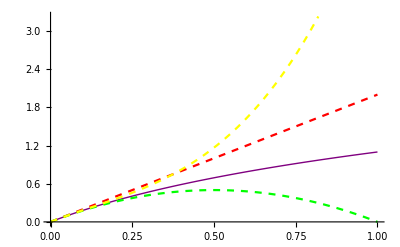

```mathematica
Plot[{f[x], lin[x,0],quad[x,0], cub[x,0]},{x,0,1}, 
	PlotStyle->{{Thick,Purple},{Dashed,Red},{ Dashed, Green}, {Dashed,Yellow}}]
```

### Exercise V1-5

#### (a) lim_(x→0) x/(tan(x))

```mathematica
h:=x/Tan[x]
Limit[h, x->0]
```

1

#### (b) lim_(x→1) (x^2-1)/(ln(x))

```mathematica
h:=(x^2-1)/Log[x]
Limit[h,x->1]
```

2

#### (c) lim_(x→1) (x^3-x^2-x+1)/(x^2-2x+1)

```mathematica
h:=(x^3-x^2-x+1)/(x^2-2x+1)
Limit[h, x->1]
```

2

#### (d) lim_(x→0) (sin(x)-x)/(cos(x)-1)

```mathematica
h:=(Sin[x]-x)/(Cos[x]-1)
Limit[h, x->0]
```

0